```mathematica
Analyze Card Games with Hypergeometric Distribution
```

```mathematica
fgrid[list_,{col1_,col2_}]:=TraditionalForm@Grid[list,Dividers->All,Spacings->{{1,1},2},Alignment->{Left,Center,{{1,1}->{Center},{1,2}->{Center}}},BaseStyle->{FontFamily->"Verdana"},Background->{None,{Lighter[Blend[{col1,col2}],.4],{Lighter[Blend[{col1,col2}],.7],GrayLevel[.9]}}},FrameStyle->Directive[Thick,White]]
```

```mathematica
dPlot[dist_,dom_,range_,label_]:=DiscretePlot[PDF[dist,k],dom,ExtentSize->2/3,PlotRange->range,AxesOrigin->{-0.2,0},BaseStyle->{FontFamily->"Verdana"},Frame->{{True,False},{True,False}},FrameLabel->{Style["number of spades",Bold,12],None},ImageSize->280,PlotLabel->Framed[Style[Grid[{{label},{dist}}],12],RoundingRadius->5,Background->LightOrange]]
```

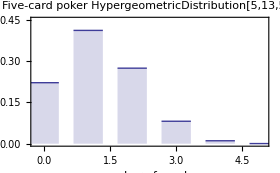
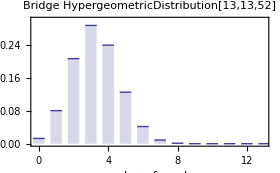
| Probability of
at least 1 spades | 0.778466
at least 2 spades | 0.367047
at least 3 spades | 0.0927671
at least 4 spades | 0.0112245
at least 5 spades | 0.000495198 |     | -Graphics-
 |  | 
  |  | 
  | Probability of
at least 1 spades | 0.987209
at least 2 spades | 0.907147
at least 3 spades | 0.701274
at least 4 spades | 0.414944
at least 5 spades | 0.176336
at least 6 spades | 0.0516443
at least 7 spades | 0.0100803
at least 8 spades | 0.00126372
at least 9 spades | 0.0000968192
at least 10 spades | 4.20788×10^-6
at least 11 spades | 9.18185×10^-8
at least 12 spades | 7.99983×10^-10
at least 13 spades | 1.57477×10^-12 |     | -Graphics-

```mathematica
Grid[{{fgrid[Join[{{" ","Probability of"}},Table[{Row[{"at least ",k," spades"}],NProbability[x≥k,x\[Distributed]HypergeometricDistribution[5,13,52]]},{k,1,5}]],{Red,Red}],"   ",dPlot[HypergeometricDistribution[5,13,52],{k,0,5},{0,0.45},"Five-card poker"]},{""},{" "},{fgrid[Join[{{" ","Probability of"}},Table[{Row[{"at least ",k," spades"}],NProbability[x≥k,x\[Distributed]HypergeometricDistribution[13,13,52]]},{k,1,13}]],{Blue,Green}],"   ",dPlot[HypergeometricDistribution[13,13,52],{k,0,13},{0,0.3},"Bridge"]}}]
```